6. Do the following tasks using Mathematica.

(a) Plot the above functions in a single graph for -1  ≤ x ≤ 1.
Hint: Use Abs[ ] function to write absolute value
Ans:

```mathematica
f[x_] = x ⅇ^(x^2);
```

```mathematica
g[x_] =  Abs[2  x];
```

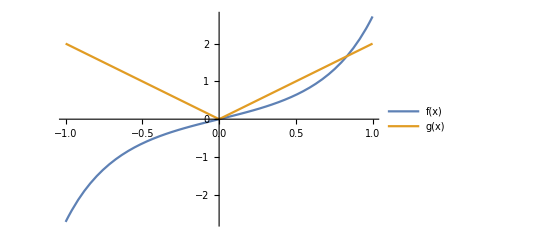

```mathematica
Plot[{f[x],g[x]},{x,-1,1},PlotLegends->"Expressions"]
```

(b) Find the limits of the integration for the area of the region enclosed by
f(x) and g(x) for -1  ≤ x ≤ 1.
Hint: Solve equations to find the intersections.
Ans:

```mathematica
Solve[{f[x]== g[x]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→√Log[2]}}

(c) Finally, do the integration to find the area
Ans:

```mathematica
NIntegrate[g[x]-f[x],{x,0,√Log[2]}]
```

0.193147